# Combine Plots

## LEP experiment

### 1996 LEP

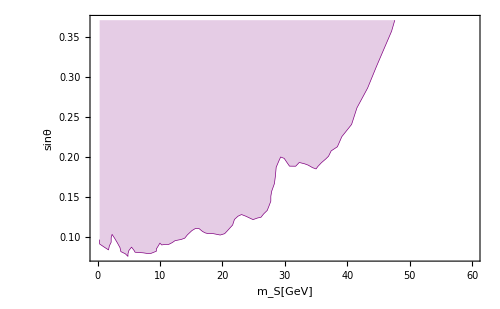

```mathematica
LEP1996data={#1,√#2}&@@@Import[NotebookDirectory[]<>"/probe/LEP1996.csv"];
LEP1996func[mS_]=Interpolation[LEP1996data,InterpolationOrder->1][mS];
LEP1996=ListLinePlot[LEP1996data,Filling->Top,BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,FrameLabel->{Style["m_S[GeV]",FontFamily->"Times",FontSize->18],Style["sinθ",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->18]},PlotRangePadding->None,ImageSize->500,PlotStyle->Directive[Purple,Thickness[0.001]]]
```

### ALEPH 2003

```mathematica
mb=4.19;
mc=1.27;
mτ=1.78;
bBR[mS_]:=(3 mb^2 Re[(mS^2-4 mb^2)^(3/2)])/(3 mb^2 Re[(mS^2-4 mb^2)^(3/2)]+3 mc^2 Re[(mS^2-4 mc^2)^(3/2)]+mτ^2 Re[(mS^2-4 mτ^2)^(3/2)]);
cBR[mS_]:=(3 mc^2 Re[(mS^2-4 mc^2)^(3/2)])/(3 mb^2 Re[(mS^2-4 mb^2)^(3/2)]+3 mc^2 Re[(mS^2-4 mc^2)^(3/2)]+mτ^2 Re[(mS^2-4 mτ^2)^(3/2)]);τBR[mS_]:=(mτ^2 Re[(mS^2-4 mτ^2)^(3/2)])/(3 mb^2 Re[(mS^2-4 mb^2)^(3/2)]+3 mc^2 Re[(mS^2-4 mc^2)^(3/2)]+mτ^2 Re[(mS^2-4 mτ^2)^(3/2)]);
bblimit[mS_]=Interpolation[Import[NotebookDirectory[]<>"./probe/LEP-ALEPH.csv"],InterpolationOrder->1][mS];
bb‵bound[mS_/;mS>=12.4]=√(bblimit[ mS]/bBR[mS]);
```

### OPAL

```mathematica
{#1,√#2}&@@@Import[NotebookDirectory[]<>"./probe/OPAL.csv"];
opalfunc[mS_]=Interpolation[{#1,√#2}&@@@Import[NotebookDirectory[]<>"./probe/OPAL.csv"]][mS];
```

```mathematica
FindRoot[bb‵bound[mS]-LEP1996func[mS],{mS,15}]
```

FindRoot::nlnum: The function value {-0.080141+bb‵bound(7.90768)} is not a list of numbers with dimensions {1} at {mS} = {7.90768}.

{mS→17.4271}

### Combine

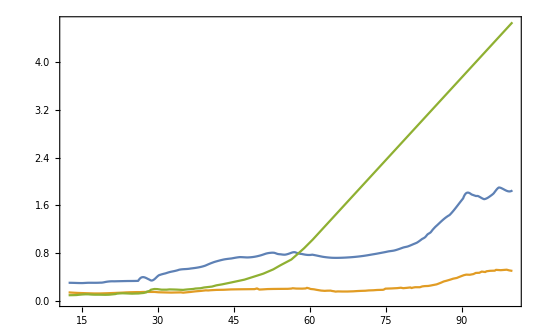

```mathematica
Plot[{opalfunc[mS],bb‵bound[mS],LEP1996func[mS]},{mS,12.4,100}]
```

OK we see that the model-independent OPAL bound is always the losest. Ignore it.

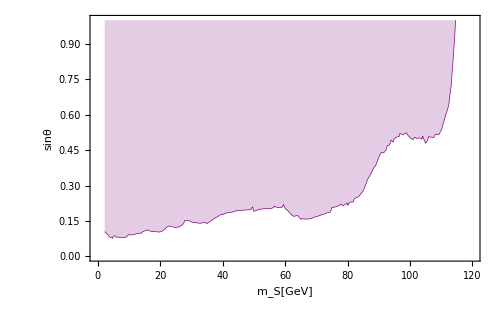

```mathematica
Combinebound[mS_/;12.4<=mS<=68.1]:=Min[LEP1996func[mS],bb‵bound[mS]]
Combinebound[mS_/;mS<12.4]:=LEP1996func[mS]
Combinebound[mS_/;mS>68.1]:=bb‵bound[mS]
LEP=Plot[Combinebound[mS],{mS,2.3,115},Filling->Top,BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,FrameLabel->{Style["m_S[GeV]",FontFamily->"Times",FontSize->18],Style["sinθ",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->18]},PlotRangePadding->None,ImageSize->500,PlotStyle->Directive[Purple,Thickness[0.001]],PlotRange->{{0,120},{0,1}},FillingStyle->Opacity[0.2]]
```

## LHCb experiment

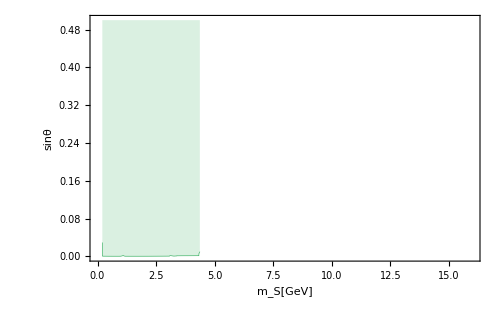

```mathematica
LHCbdata={#1, √#2}& @@@Import[NotebookDirectory[]<>"probe/LHCb.csv"];
LHCb=ListLinePlot[LHCbdata,Filling->Top,BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,FrameLabel->{Style["m_S[GeV]",FontFamily->"Times",FontSize->18],Style["sinθ",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->18]},PlotRangePadding->None,ImageSize->500,PlotStyle->Directive[ColorData[97,15],Thickness[0.001]],PlotRange->{{0,16},{0,0.5}}]
```

## Exotic Decay

Imort data. The boundary depends on f and thus on c. Thus the bound is derived only at the last step when we try to make the plot.

```mathematica
prospectdata=Import[NotebookDirectory[]<>"probe/Exoticdecay.csv"];
prospectfunc[mS_]:=Interpolation[prospectdata][mS];
Currentdata1=Import[NotebookDirectory[]<>"probe/ExoticDecayCurrent1.csv"];
Currentdata2=Import[NotebookDirectory[]<>"probe/ExoticDecayCurrent2.csv"];
Higgsfactorydata=Import[NotebookDirectory[]<>"probe/Higgsfactory.csv"];
Higgsfactoryfunc[mS_]:=Interpolation[Higgsfactorydata][mS]
Higgsfactorydata2=Import[NotebookDirectory[]<>"probe/Higgsfactory02.csv"];
Higgsfactoryfunc2[mS_]:=Interpolation[Higgsfactorydata2][mS]
Currentfunc1[mS_]:=Interpolation[Currentdata1][mS];
Currentfunc2[mS_]:=Interpolation[Currentdata2][mS];
```

## Kaon decay

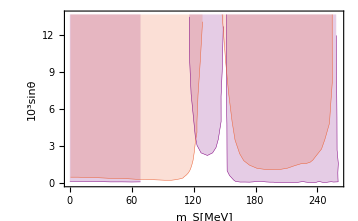

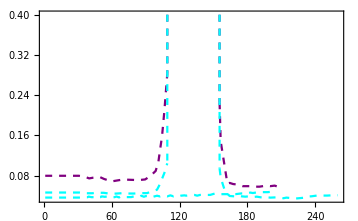

```mathematica
NA621={#1,1000*√(#2/(1.7*10^-3))}& @@@Import[NotebookDirectory[]<>"./probe/NA62-1.csv"];
NA622={#1,1000*√(#2/(1.7*10^-3))}& @@@Import[NotebookDirectory[]<>"./probe/NA62-2.csv"];
NA623={#1,1000*√(#2/(1.7*10^-3))}& @@@Import[NotebookDirectory[]<>"./probe/NA62-3.csv"];
E9491={#1,1000*√(#2/(1.7*10^-3))}& @@@Import[NotebookDirectory[]<>"./probe/E949.csv"];
E9492={#1,1000*√(#2/(1.7*10^-3))}& @@@Import[NotebookDirectory[]<>"./probe/E949-2.csv"];
NA62‵run2={#1*1000,1000*√#2}&@@@Import[NotebookDirectory[]<>"./probe/NA62-run2.csv"];
NA62‵run202={#1*1000,1000*√#2}&@@@Import[NotebookDirectory[]<>"./probe/NA62-run2-02.csv"];
HIKE1={#1*1000,1000*√#2}&@@@Import[NotebookDirectory[]<>"./probe/HIKE-1.csv"];
HIKE102={#1*1000,1000*√#2}&@@@Import[NotebookDirectory[]<>"./probe/HIKE-1-02.csv"];
HIKE2={#1*1000,1000*√#2}&@@@Import[NotebookDirectory[]<>"./probe/HIKE-2.csv"];
NA62run201=Show[ListLinePlot[NA62‵run2,PlotStyle->Directive[Dashed,Purple],PlotRange->Full],ContourPlot[x==Max[NA62‵run2[[All,1]]],{x,0,200},{y,NA62‵run2[[-1]][[2]],0.4},ContourStyle->Directive[Purple,Dashed]],PlotRange->Full];
NA62run202=Show[ListLinePlot[NA62‵run202,PlotStyle->Directive[Dashed,Purple],PlotRange->Full],ContourPlot[x==Min[NA62‵run202[[All,1]]],{x,0,200},{y,NA62‵run202[[1]][[2]],0.4},ContourStyle->Directive[Purple,Dashed]],PlotRange->Full];
HIKE101=Show[ListLinePlot[HIKE1,PlotStyle->Directive[Dashed,Cyan],PlotRange->Full],ContourPlot[x==Max[HIKE1[[All,1]]],{x,0,200},{y,HIKE1[[-1]][[2]],0.4},ContourStyle->Directive[Cyan,Dashed]],PlotRange->Full];
HIKE102=Show[ListLinePlot[HIKE102,PlotStyle->Directive[Dashed,Cyan],PlotRange->Full],ContourPlot[x==Min[HIKE102[[All,1]]],{x,0,200},{y,HIKE102[[1]][[2]],0.4},ContourStyle->Directive[Cyan,Dashed]],PlotRange->Full];
Kaondecay1=ListLinePlot[{NA621,NA622,NA623,E9491,E9492},Filling->Top,BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,FrameLabel->{Style["m_S[MeV]",FontFamily->"Times",FontSize->18],Style["10^3sinθ",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->18]},PlotStyle->{Directive[Purple,Thickness[0.001]],Directive[Purple,Thickness[0.001]],Directive[Purple,Thickness[0.001]],Directive[ColorData[97,4],Thickness[0.001]],Directive[ColorData[97,4],Thickness[0.001]]}]
HIKE2plot=ListLinePlot[HIKE2,PlotStyle->Directive[Dashed,Cyan],PlotRange->Full];
Kaondecay2=Show[NA62run201,NA62run202,HIKE101,HIKE102,HIKE2plot,PlotRange->Full]
```

## CMB probe

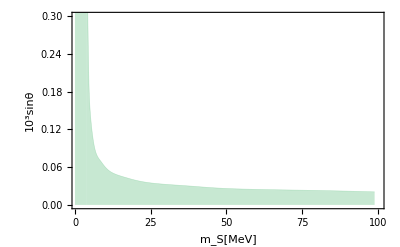

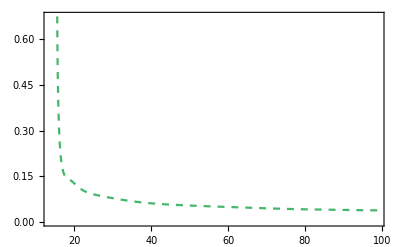

```mathematica
CMBS4data={#1,1000#2}&@@@Import[NotebookDirectory[]<>"./probe/CMB-S4.csv"];
CMBfunc[mS_]:=Interpolation[CMBS4data][mS]
perspect‵CMB‵data=SortBy[{#1,1000#2}&@@@Import[NotebookDirectory[]<>"./probe/CMB-perspective.csv"],First];
Planck01=Plot[y=10,{x,0,Min[{#1}&@@@CMBS4data]},Filling->Bottom,PlotStyle->{ColorData[97,15],Opacity[0.3]},FillingStyle->Opacity[0.3]];
Planck02=ListLinePlot[CMBS4data,PlotRange->Full,InterpolationOrder->3,AxesOrigin->{1,0.},Filling->Bottom,BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,FrameLabel->{Style["m_S[MeV]",FontFamily->"Times",FontSize->18],Style["10^3sinθ",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->18]},PlotRangePadding->None,PlotStyle->{ColorData[97,15],Opacity[0.3],Thickness[0.001]},FillingStyle->Opacity[0.3]];
Planck=Show[Planck02,Planck01,PlotRange->{{1,100},{0,0.3}}]
CMB‵perspect=ListLinePlot[perspect‵CMB‵data,InterpolationOrder->3,PlotRange->Full,PlotStyle->Directive[Dashed,ColorData[97,15]]]
```

## Supernovae

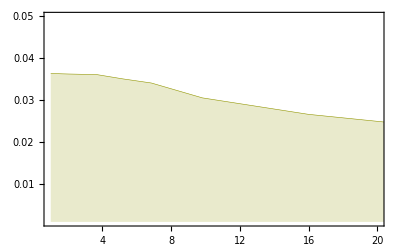

```mathematica
SNdata={#1,1000*#2}&@@@Import[NotebookDirectory[]<>"probe/SN.csv"];
SN=ListLinePlot[SNdata,Filling->Bottom,PlotStyle->{Directive[Thickness[0.001],ColorData[97,10]]},PlotRange->{{1,20},{0.001,0.05}}]
```

## SFOPT bound

```mathematica
c3‵δ2pi5‵strength‵data2={#1,#2,#3+0.3}&@@@c3‵δ2pi5‵strength‵data;
p2=ListContourPlot[c3‵δ2pi5‵strength‵data2,Contours->{1.0},ContourShading->None];
p1=ListContourPlot[c3‵δ2pi5‵strength‵data,Contours->{1.0},ContourShading->None];
Show[p1,p2]
```

ListContourPlot::arrayerr: c3‵δ2pi5‵strength‵data must be a valid array.

Show::gcomb: Could not combine the graphics objects in Show[ListContourPlot[c3‵δ2pi5‵strength‵data,Contours→{1.},ContourShading→None],ListContourPlot[c3‵δ2pi5‵strength‵data,Contours→{1.},ContourShading→None]].

Show[ListContourPlot[c3‵δ2pi5‵strength‵data,Contours→{1.},ContourShading→None],ListContourPlot[c3‵δ2pi5‵strength‵data,Contours→{1.},ContourShading→None]]

```mathematica
3*Sin[π/5]//N
3*Sin[(2π)/5]//N
```

1.76336

2.85317

```mathematica
p1=ListContourPlot[c3‵δ2pi5‵strength‵data,Contours->{1.0},ContourShading->None];
p2=ListContourPlot[c3‵δ2pi5‵strength‵data,Contours->{0.7},ContourShading->None];
Show[p1,p2,PlotRange->{Full,{0,0.2}}]
```

ListContourPlot::arrayerr: c3‵δ2pi5‵strength‵data must be a valid array.

Show::gcomb: Could not combine the graphics objects in Show[ListContourPlot[c3‵δ2pi5‵strength‵data,Contours→{1.},ContourShading→None],ListContourPlot[c3‵δ2pi5‵strength‵data,Contours→{0.7},ContourShading→None],PlotRange→{Full,{0,0.2}}].

Show[ListContourPlot[c3‵δ2pi5‵strength‵data,Contours→{1.},ContourShading→None],ListContourPlot[c3‵δ2pi5‵strength‵data,Contours→{0.7},ContourShading→None],PlotRange→{Full,{0,0.2}}]

```mathematica
p1=ListContourPlot[c30‵δ2pi5‵strength‵data,Contours->{1.2},ContourShading->None];
p2=ListContourPlot[c30‵δ2pi5‵strength‵data,Contours->{1.2*0.7},ContourShading->None];
Show[p1,p2,PlotRange->{Full,{0,0.3}}]
```

ListContourPlot::arrayerr: c30‵δ2pi5‵strength‵data must be a valid array.

Show::gcomb: Could not combine the graphics objects in Show[ListContourPlot[c30‵δ2pi5‵strength‵data,Contours→{1.2},ContourShading→None],ListContourPlot[c30‵δ2pi5‵strength‵data,Contours→{0.84},ContourShading→None],PlotRange→{Full,{0,0.3}}].

Show[ListContourPlot[c30‵δ2pi5‵strength‵data,Contours→{1.2},ContourShading→None],ListContourPlot[c30‵δ2pi5‵strength‵data,Contours→{0.84},ContourShading→None],PlotRange→{Full,{0,0.3}}]

```mathematica
p1=ListContourPlot[c3‵δpi5‵strength‵data,Contours->{1.},ContourShading->None];
p2=ListContourPlot[c3‵δpi5‵strength‵data,Contours->{0.7},ContourShading->None];
Show[p1,p2,PlotRange->{Full,{0,0.2}}]
```

ListContourPlot::arrayerr: c3‵δpi5‵strength‵data must be a valid array.

Show::gcomb: Could not combine the graphics objects in Show[ListContourPlot[c3‵δpi5‵strength‵data,Contours→{1.},ContourShading→None],ListContourPlot[c3‵δpi5‵strength‵data,Contours→{0.7},ContourShading→None],PlotRange→{Full,{0,0.2}}].

Show[ListContourPlot[c3‵δpi5‵strength‵data,Contours→{1.},ContourShading→None],ListContourPlot[c3‵δpi5‵strength‵data,Contours→{0.7},ContourShading→None],PlotRange→{Full,{0,0.2}}]

```mathematica
p1=ListContourPlot[c30‵δpi5‵strength‵data,Contours->{1.2},ContourShading->None];
p2=ListContourPlot[c30‵δpi5‵strength‵data,Contours->{0.7*1.2},ContourShading->None];
Show[p1,p2,PlotRange->{Full,{0,0.4}}]
```

ListContourPlot::arrayerr: c30‵δpi5‵strength‵data must be a valid array.

Show::gcomb: Could not combine the graphics objects in Show[ListContourPlot[c30‵δpi5‵strength‵data,Contours→{1.2},ContourShading→None],ListContourPlot[c30‵δpi5‵strength‵data,Contours→{0.84},ContourShading→None],PlotRange→{Full,{0,0.4}}].

Show[ListContourPlot[c30‵δpi5‵strength‵data,Contours→{1.2},ContourShading→None],ListContourPlot[c30‵δpi5‵strength‵data,Contours→{0.84},ContourShading→None],PlotRange→{Full,{0,0.4}}]

### GeV scale

```mathematica
c30‵δ2pi5‵data=Import[NotebookDirectory[]<>"/phase_transition/output/c30_delta_2pi5_GeV_out.csv"];
c30‵δ2pi5‵strength‵data={#1,#2,1.2*#8}&@@@c30‵δ2pi5‵data;
c3‵δ2pi5‵data=Import[NotebookDirectory[]<>"/phase_transition/output/c3_delta_2pi5_GeV_out.csv"];
c3‵δ2pi5‵strength‵data={#1,#2,1.2*#8}&@@@c3‵δ2pi5‵data;
c30‵δpi5‵data=Import[NotebookDirectory[]<>"/phase_transition/output/c30_delta_pi5_GeV_out.csv"];
c30‵δpi5‵strength‵data={#1,#2,1.2*#8}&@@@c30‵δpi5‵data;
c3‵δpi5‵data=Import[NotebookDirectory[]<>"/phase_transition/output/c3_delta_pi5_GeV_out.csv"];
c3‵δpi5‵strength‵data={#1,#2,1.2*#8}&@@@c3‵δpi5‵data;
c12‵δpi20‵data=Import[NotebookDirectory[]<>"/phase_transition/output/c12_delta_pi20_GeV_out.csv"];
c12‵δpi20‵strength‵data={#1,#2,1.2*#8}&@@@c12‵δpi20‵data;
c15‵δpi20‵data=Import[NotebookDirectory[]<>"/phase_transition/output/c15_delta_pi20_GeV_out.csv"];
c15‵δpi20‵strength‵data={#1,#2,1.2*#8}&@@@c15‵δpi20‵data;
```

Discuss some naturalness requirement here:

```mathematica
c3‵δ2pi5‵natural‵data={#1,#2,√((16 π^2#6 #7)/#4)}&@@@c3‵δ2pi5‵data;
c3‵δpi5‵natural‵data={#1,#2,√((16 π^2#6 #7)/#4)}&@@@c3‵δpi5‵data;
```

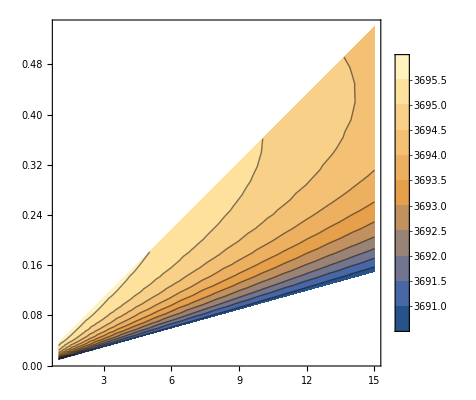

```mathematica
ListContourPlot[c3‵δ2pi5‵natural‵data,PlotLegends->Automatic]
```

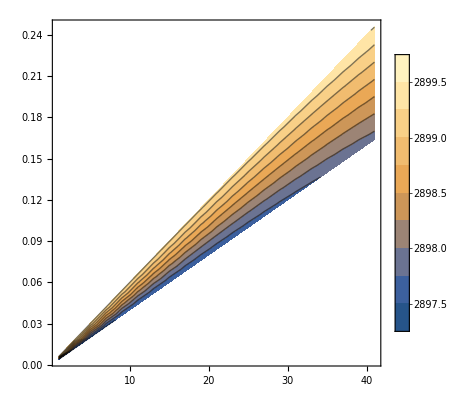

```mathematica
ListContourPlot[c3‵δpi5‵natural‵data,PlotLegends->Automatic]
```

```mathematica
c30‵δ2pi5‵strength‵plot=ListLinePlot[Cases[ListContourPlot[c30‵δ2pi5‵strength‵data,Contours->{1.0},ContourShading->None,PlotRange->Full][[1]]//Normal,Line[z_]->z,Infinity],Filling->Bottom,FillingStyle->Opacity[0.1],PlotRange->Full];
c3‵δ2pi5‵strength‵plot=ListLinePlot[Cases[ListContourPlot[c3‵δ2pi5‵strength‵data,Contours->{1.0},ContourShading->None,PlotRange->Full][[1]]//Normal,Line[z_]->z,Infinity],Filling->Bottom,FillingStyle->Opacity[0.3],PlotRange->Full];
c3‵δpi5‵strength‵plot=ListLinePlot[Cases[ListContourPlot[c3‵δpi5‵strength‵data,Contours->{1.0},ContourShading->None,PlotRange->Full][[1]]//Normal,Line[z_]->z,Infinity],Filling->Bottom,FillingStyle->Opacity[0.3],PlotRange->Full];
c30‵δpi5‵strength‵plot=ListLinePlot[Cases[ListContourPlot[c30‵δpi5‵strength‵data,Contours->{1.0},ContourShading->None,PlotRange->Full][[1]]//Normal,Line[z_]->z,Infinity],Filling->Bottom,FillingStyle->Opacity[0.1],PlotRange->Full];
c12‵δpi20‵strength‵plot=ListLinePlot[Cases[ListContourPlot[c12‵δpi20‵strength‵data,Contours->{1.0},ContourShading->None,PlotRange->Full][[1]]//Normal,Line[z_]->z,Infinity],Filling->Bottom,FillingStyle->Opacity[0.3],PlotRange->Full];
c15‵δpi20‵strength‵plot=ListLinePlot[Cases[ListContourPlot[c15‵δpi20‵strength‵data,Contours->{1.0},ContourShading->None,PlotRange->Full][[1]]//Normal,Line[z_]->z,Infinity],Filling->Bottom,FillingStyle->Opacity[0.1],PlotRange->Full];
```

### MeV

```mathematica
c30‵δ2pi5‵MeV‵data=Import[NotebookDirectory[]<>"/phase_transition/output/c30_delta_2pi5_MeV_out.csv"];
c30‵δ2pi5‵MeV‵strength‵data={#1*1000,#2*1000,1.2*#8}&@@@c30‵δ2pi5‵MeV‵data;
c3‵δ2pi5‵MeV‵data=Import[NotebookDirectory[]<>"/phase_transition/output/c3_delta_2pi5_MeV_out.csv"];
c3‵δ2pi5‵MeV‵strength‵data={#1*1000,#2*1000,1.2*#8}&@@@c3‵δ2pi5‵MeV‵data;
c3‵δpi5‵MeV‵data=Import[NotebookDirectory[]<>"/phase_transition/output/c3_delta_pi5_MeV_out.csv"];
c3‵δpi5‵MeV‵strength‵data={#1*1000,#2*1000,1.2*#8}&@@@c3‵δpi5‵MeV‵data;
c30‵δpi5‵MeV‵data=Import[NotebookDirectory[]<>"/phase_transition/output/c30_delta_pi5_MeV_out.csv"];
c30‵δpi5‵MeV‵strength‵data={#1*1000,#2*1000,1.2*#8}&@@@c30‵δpi5‵MeV‵data;
c12‵δpi20‵MeV‵data=Import[NotebookDirectory[]<>"/phase_transition/output/c12_delta_pi20_MeV_out.csv"];
c12‵δpi20‵MeV‵strength‵data={#1*1000,#2*1000,1.2*#8}&@@@c12‵δpi20‵MeV‵data;
c15‵δpi20‵MeV‵data=Import[NotebookDirectory[]<>"/phase_transition/output/c15_delta_pi20_MeV_out.csv"];
c15‵δpi20‵MeV‵strength‵data={#1*1000,#2*1000,1.2*#8}&@@@c15‵δpi20‵MeV‵data;
```

```mathematica
c30‵δ2pi5‵MeV‵strength‵plot=ListLinePlot[Cases[ListContourPlot[c30‵δ2pi5‵MeV‵strength‵data,Contours->{1.0},ContourShading->None,PlotRange->Full][[1]]//Normal,Line[z_]->z,Infinity],Filling->Bottom,FillingStyle->Opacity[0.1],PlotRange->Full];
c3‵δ2pi5‵MeV‵strength‵plot=ListLinePlot[Cases[ListContourPlot[c3‵δ2pi5‵MeV‵strength‵data,Contours->{1.0},ContourShading->None,PlotRange->Full][[1]]//Normal,Line[z_]->z,Infinity],Filling->Bottom,FillingStyle->Opacity[0.2],PlotRange->Full,InterpolationOrder->3];
c30‵δpi5‵MeV‵strength‵plot=ListLinePlot[Cases[ListContourPlot[c30‵δpi5‵MeV‵strength‵data,Contours->{1.0},ContourShading->None,PlotRange->Full][[1]]//Normal,Line[z_]->z,Infinity],Filling->Bottom,FillingStyle->Opacity[0.1],PlotRange->Full];
c3‵δpi5‵MeV‵strength‵plot=ListLinePlot[Cases[ListContourPlot[c3‵δpi5‵MeV‵strength‵data,Contours->{1.0},ContourShading->None,PlotRange->Full][[1]]//Normal,Line[z_]->z,Infinity],Filling->Bottom,FillingStyle->Opacity[0.2],PlotRange->Full];
c12‵δpi20‵MeV‵strength‵plot=ListLinePlot[Cases[ListContourPlot[c12‵δpi20‵MeV‵strength‵data,Contours->{1.0},ContourShading->None,PlotRange->Full][[1]]//Normal,Line[z_]->z,Infinity],Filling->Bottom,FillingStyle->Opacity[0.2],PlotRange->Full];
c15‵δpi20‵MeV‵strength‵plot=ListLinePlot[Cases[ListContourPlot[c15‵δpi20‵MeV‵strength‵data,Contours->{1.0},ContourShading->None,PlotRange->Full][[1]]//Normal,Line[z_]->z,Infinity],Filling->Bottom,FillingStyle->Opacity[0.1],PlotRange->Full];
```

## Lower limit on f

```mathematica
c3‵δpi5‵f‵data=Import[NotebookDirectory[]<>"./model_setup/output/c3_delta_pi5_f.csv"];
c3‵δ2pi5‵f‵data=Import[NotebookDirectory[]<>"./model_setup/output/c3_delta_2pi5_f.csv"];
c12‵δpi20‵f‵data=Import[NotebookDirectory[]<>"./model_setup/output/c12_delta_pi20_f.csv"];
c15‵δpi20‵f‵data={#1,#2,1.5/1.2#3}&@@@c12‵δpi20‵f‵data;
```

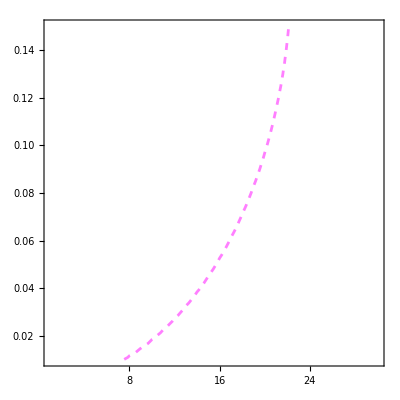

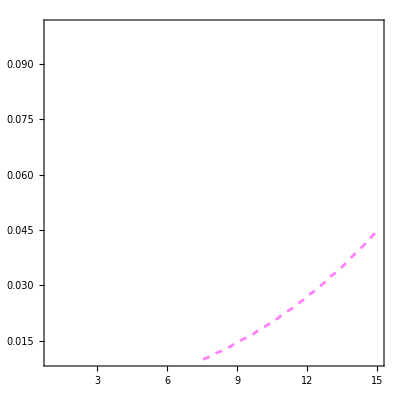

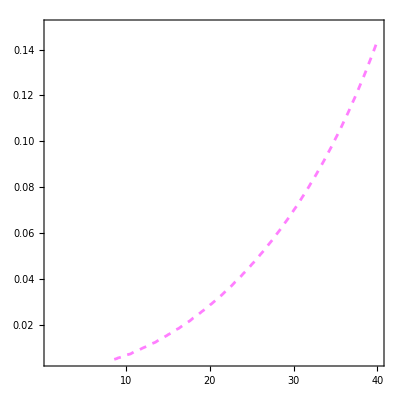

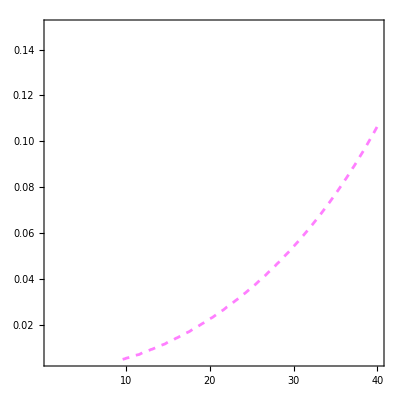

```mathematica
c3‵δpi5‵f‵plot=ListContourPlot[c3‵δpi5‵f‵data,Contours->{1000},ContourShading->None,ContourStyle->Directive[Magenta,Thickness[0.005],Dashed]]
c3‵δ2pi5‵f‵plot=ListContourPlot[c3‵δ2pi5‵f‵data,Contours->{1000},ContourShading->None,ContourStyle->Directive[Magenta,Thickness[0.005],Dashed]]
c12‵δpi20‵f‵plot=ListContourPlot[c12‵δpi20‵f‵data,Contours->{1000},ContourShading->None,ContourStyle->Directive[Magenta,Thickness[0.005],Dashed]]
c15‵δpi20‵f‵plot=ListContourPlot[c15‵δpi20‵f‵data,Contours->{1000},ContourShading->None,ContourStyle->Directive[Magenta,Thickness[0.005],Dashed]]
```

## EDM and BAU

```mathematica
v=246.22;
α2=0.65^2/(4π);
s=2 π^2/45*100;
ΔS[A_,μSsq_,f_,δ_,h_,T_]:=f (ArcTan[(A(3(h^2-v^2)+T^2)Sin[δ])/(6f μSsq+A(3(h^2-v^2)+T^2)Cos[δ])]-ArcTan[(A(3(-v^2)+T^2)Sin[δ])/(6f μSsq+A(3(-v^2)+T^2)Cos[δ])]);
(*Gives the rescaling between M and f to get successful baryogenesis*)
c30‵δ2pi5‵BAU‵data={#1,#2,3*20*α2^5/(#7(8.7*10^-11)*s)ΔS[#4,#6,#7,2 π/5,0.3*#9,#9]}&@@@c30‵δ2pi5‵data;
c3‵δ2pi5‵BAU‵data={#1,#2,3*20*α2^5/(#7*s*(8.7*10^-11))ΔS[#4,#6,#7,2 π/5,0.3*#9,#9]}&@@@c3‵δ2pi5‵data;
c30‵δpi5‵BAU‵data={#1,#2,3*20*α2^5/(#7*s*(8.7*10^-11))ΔS[#4,#6,#7,π/5,0.3*#9,#9]}&@@@c30‵δpi5‵data;
c3‵δpi5‵BAU‵data={#1,#2,3*20*α2^5/(#7*s*(8.7*10^-11))ΔS[#4,#6,#7,π/5,0.3*#9,#9]}&@@@c3‵δpi5‵data;
c12‵δpi20‵BAU‵data={#1,#2,3*20*α2^5/(#7*s*(8.7*10^-11))ΔS[#4,#6,#7,π/20,0.3*#9,#9]}&@@@c12‵δpi20‵data;
c15‵δpi20‵BAU‵data={#1,#2,3*20*α2^5/(#7*s*(8.7*10^-11))ΔS[#4,#6,#7,π/20,0.3*#9,#9]}&@@@c15‵δpi20‵data;
```

```mathematica
c3‵δ2π5‵EDM‵data=Import[NotebookDirectory[]<>"./model_setup/output/c3_delta_2pi5_edm.csv"];
c30‵δ2π5‵EDM‵data=Import[NotebookDirectory[]<>"./model_setup/output/c30_delta_2pi5_edm.csv"];
c3‵δπ5‵EDM‵data=Import[NotebookDirectory[]<>"./model_setup/output/c3_delta_pi5_edm.csv"];
c30‵δπ5‵EDM‵data=Import[NotebookDirectory[]<>"./model_setup/output/c30_delta_pi5_edm.csv"];
c12‵δπ20‵EDM‵data=Import[NotebookDirectory[]<>"./model_setup/output/c12_delta_pi20_edm.csv"];
c15‵δπ20‵EDM‵data=Import[NotebookDirectory[]<>"./model_setup/output/c15_delta_pi20_edm.csv"];
```

Consider S couples with U(1) gauge boson.

```mathematica
c3‵δ2π5‵EDM‵SBB‵data={#1,#2,#3*0.303^2/0.65^2*Log[vnum^2/#1^2]}&@@@Import[NotebookDirectory[]<>"./model_setup/output/c3_delta_2pi5_edm.csv"];
c30‵δ2π5‵EDM‵SBB‵data={#1,#2,#3*0.303^2/0.65^2*Log[vnum^2/#1^2]}&@@@Import[NotebookDirectory[]<>"./model_setup/output/c30_delta_2pi5_edm.csv"];
c3‵δπ5‵EDM‵SBB‵data={#1,#2,#3*0.303^2/0.65^2*Log[vnum^2/#1^2]}&@@@Import[NotebookDirectory[]<>"./model_setup/output/c3_delta_pi5_edm.csv"];
c30‵δπ5‵EDM‵SBB‵data={#1,#2,#3*0.303^2/0.65^2*Log[vnum^2/#1^2]}&@@@Import[NotebookDirectory[]<>"./model_setup/output/c30_delta_pi5_edm.csv"];
c12‵δπ20‵EDM‵SBB‵data={#1,#2,#3*0.303^2/0.65^2*Log[vnum^2/#1^2]}&@@@Import[NotebookDirectory[]<>"./model_setup/output/c12_delta_pi20_edm.csv"];
c15‵δπ20‵EDM‵SBB‵data={#1,#2,#3*0.303^2/0.65^2*Log[vnum^2/#1^2]}&@@@Import[NotebookDirectory[]<>"./model_setup/output/c15_delta_pi20_edm.csv"];
```

```mathematica
ListContourPlot[c3‵δ2π5‵EDM‵SBB‵data,Contours->{10^-29},ContourShading->None]
```

-Graphics-

InterpolatingFunction::dmval: Input value {9.,0.153} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9.,0.162} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9.,0.171} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

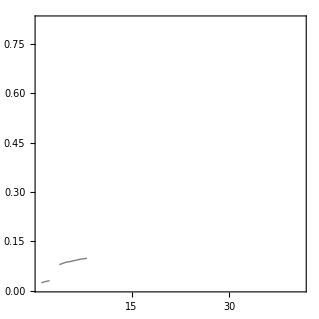

```mathematica
c30‵δpi5‵EDM‵func[mS_,sinθ_]=Interpolation[c30‵δπ5‵EDM‵data][mS,sinθ];
c30‵δπ5‵EDM‵data‵new={#1,#2,(c30‵δpi5‵EDM‵func[#1,#2])/#3}&@@@c30‵δpi5‵BAU‵data;
ListContourPlot[c30‵δπ5‵EDM‵data‵new,Contours->{1*10^-30,10^-29},ContourShading->None]
```

## Combine

### δ=2π/5, GeV scale

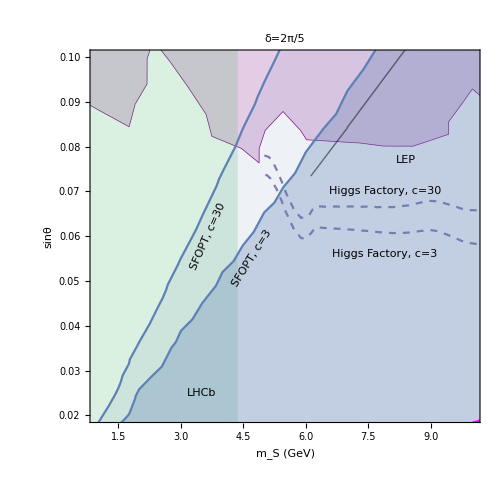

```mathematica
v=246.22;
mhpole=125.13;
ΓSM=4.07*10^-3;(*GeV*)
δ=(2π)/5;
A[mS_,sinθ_]:=((mhpole^2-mS^2)sinθ √(1-sinθ^2))/(v Sin[δ]);
λhL[mS_,sinθ_]:=((1-sinθ^2)mhpole^2+sinθ^2 mS^2)/(2 v^2);
μSsq[mS_,sinθ_]:=1/2(mhpole^2+mS^2-(mhpole^2-mS^2)(1-2 sinθ^2));
f[mS_,sinθ_]=3 A[mS,sinθ]/μSsq[mS,sinθ] v^2 Sin[δ];
ghSS[mS_,sinθ_]:=-1/4 A[mS,sinθ]sinθ(1+3(1-2 sinθ^2))Sin[δ]+3λhL[mS,sinθ]v sinθ^2 √(1-sinθ^2)+A[mS,sinθ]/f[mS,sinθ] v (1/2(√(1-sinθ^2))^3-sinθ^2 √(1-sinθ^2))Cos[δ];
ΓhSS[mS_,sinθ_]:=ghSS[mS,sinθ]^2/(32π mhpole)√(1-4 mS^2/mhpole^2);
BRhSS[mS_,sinθ_]:=ΓhSS[mS,sinθ]/(ΓSM+ΓhSS[mS,sinθ]);
exotic1=RegionPlot[BRhSS[mS,sinθ]>=Currentfunc1[mS],{mS,1.1,12.5},{sinθ,0,0.25},PlotStyle->Directive[Opacity[0.2],ColorData[97,4]],BoundaryStyle->Directive[Thickness[0.001],ColorData[97,4]]];
exoticprosp=ContourPlot[BRhSS[mS,sinθ]==prospectfunc[mS],{mS,2,40},{sinθ,0,0.4},ContourStyle->Directive[Dashed,ColorData[97,4]]];
Higgsfactory2=ContourPlot[BRhSS[mS,sinθ]==Higgsfactoryfunc2[mS],{mS,4.97,10.1},{sinθ,0.,0.1},ContourStyle->Directive[Dashed,ColorData[97,5]]];
f[mS_,sinθ_]=30 A[mS,sinθ]/μSsq[mS,sinθ] v^2 Sin[δ];
ghSS[mS_,sinθ_]:=-1/4 A[mS,sinθ]sinθ(1+3(1-2 sinθ^2))Sin[δ]+3λhL[mS,sinθ]v sinθ^2 √(1-sinθ^2)+A[mS,sinθ]/f[mS,sinθ] v (1/2(√(1-sinθ^2))^3-sinθ^2 √(1-sinθ^2))Cos[δ];
ΓhSS[mS_,sinθ_]:=ghSS[mS,sinθ]^2/(32π mhpole)√(1-4 mS^2/mhpole^2);
BRhSS[mS_,sinθ_]:=ΓhSS[mS,sinθ]/(ΓSM+ΓhSS[mS,sinθ]);
exotic1‵30=RegionPlot[BRhSS[mS,sinθ]>=Currentfunc1[mS],{mS,1.1,12.5},{sinθ,0,0.25},PlotStyle->Directive[Opacity[0.2],ColorData[97,4]],BoundaryStyle->Directive[Thickness[0.001],ColorData[97,4]]];
exoticprosp‵30=ContourPlot[BRhSS[mS,sinθ]==prospectfunc[mS],{mS,2,40},{sinθ,0,0.4},ContourStyle->Directive[Dashed,ColorData[97,4]]];
Higgsfactory2‵30=ContourPlot[BRhSS[mS,sinθ]==Higgsfactoryfunc2[mS],{mS,4.97,10.1},{sinθ,0.,0.1},ContourStyle->Directive[Dashed,ColorData[97,5]]];
Show[LEP1996,LHCb,Higgsfactory2,Higgsfactory2‵30,c30‵δ2pi5‵strength‵plot,c3‵δ2pi5‵strength‵plot,c3‵δ2pi5‵f‵plot,p2,PlotRange->{{1,10},{0.02,0.1}},BaseStyle->{FontSize->22,FontFamily->"Times"},Frame->True,BoundaryStyle->None,FrameLabel->{Style["m_S (GeV)",FontFamily->"Times",FontSize->24],Style["sinθ",FontFamily->"Times",FontSize->24]},LabelStyle->{Black},FrameTicksStyle->Directive[FontFamily->"Times",FontSize->24],PlotRangePadding->None,ImageSize->500,AspectRatio->1,PlotLabel->Style["δ=2π/5",FontFamily->"Times",FontSize->26],Epilog->{Inset[Rotate[Framed[Style["SFOPT, c=3",FontFamily->"Times",FontSize->24,FontColor->ColorData[97,1]],FrameStyle->None],58 Degree],{4.7,0.055}],Inset[Rotate[Framed[Style["SFOPT, c=30",FontFamily->"Times",FontSize->24,FontColor->ColorData[97,1]],FrameStyle->None],66 Degree],{3.65,0.06}],Inset[Rotate[Framed[Style["Higgs Factory, c=3",ColorData[97,5],FontSize->22],FrameStyle->None],0Degree],{7.9,0.056}],Inset[Rotate[Framed[Style["Higgs Factory, c=30",ColorData[97,5],FontSize->22],FrameStyle->None],0Degree],{7.9,0.07}],Inset[Rotate[Framed[Style["LEP",Purple,FontSize->22],FrameStyle->None],0Degree],{8.4,0.077}],Inset[Rotate[Framed[Style["LHCb",ColorData[97,15],FontSize->22],FrameStyle->None],0Degree],{3.5,0.025}]}]
```

### δ=π/5, GeV scale

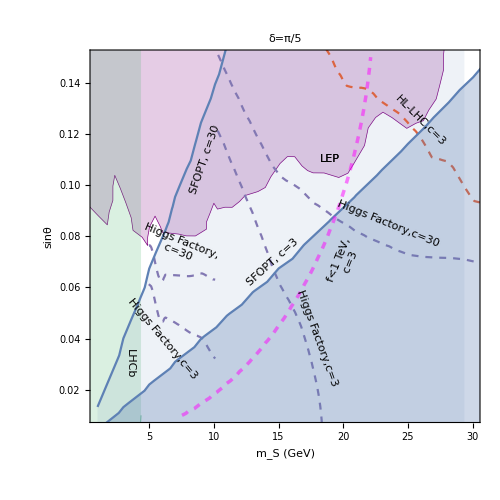

```mathematica
v=246.22;
mhpole=125.13;
ΓSM=4.07*10^-3;(*GeV*)
δ=π/5;
A[mS_,sinθ_]:=((mhpole^2-mS^2)sinθ √(1-sinθ^2))/(v Sin[δ]);
λhL[mS_,sinθ_]:=((1-sinθ^2)mhpole^2+sinθ^2 mS^2)/(2 v^2);
μSsq[mS_,sinθ_]:=1/2(mhpole^2+mS^2-(mhpole^2-mS^2)(1-2 sinθ^2));
f[mS_,sinθ_]=3 A[mS,sinθ]/μSsq[mS,sinθ] v^2 Sin[δ];
ghSS[mS_,sinθ_]:=-1/4 A[mS,sinθ]sinθ(1+3(1-2 sinθ^2))Sin[δ]+3λhL[mS,sinθ]v sinθ^2 √(1-sinθ^2)+A[mS,sinθ]/f[mS,sinθ] v (1/2(√(1-sinθ^2))^3-sinθ^2 √(1-sinθ^2))Cos[δ];
ΓhSS[mS_,sinθ_]:=ghSS[mS,sinθ]^2/(32π mhpole)√(1-4 mS^2/mhpole^2);
BRhSS[mS_,sinθ_]:=ΓhSS[mS,sinθ]/(ΓSM+ΓhSS[mS,sinθ]);
exoticprosp=ContourPlot[BRhSS[mS,sinθ]==prospectfunc[mS],{mS,17,40},{sinθ,0,0.4},ContourStyle->Directive[Dashed,ColorData[97,4]]];
Higgsfactory=ContourPlot[BRhSS[mS,sinθ]==Higgsfactoryfunc[mS],{mS,10.3,40},{sinθ,0.,0.25},ContourStyle->Directive[Dashed,ColorData[97,5]]];
Higgsfactory2=ContourPlot[BRhSS[mS,sinθ]==Higgsfactoryfunc2[mS],{mS,4.97,10.1},{sinθ,0.,0.1},ContourStyle->Directive[Dashed,ColorData[97,5]]];
f[mS_,sinθ_]=30 A[mS,sinθ]/μSsq[mS,sinθ] v^2 Sin[δ];
ghSS[mS_,sinθ_]:=-1/4 A[mS,sinθ]sinθ(1+3(1-2 sinθ^2))Sin[δ]+3λhL[mS,sinθ]v sinθ^2 √(1-sinθ^2)+A[mS,sinθ]/f[mS,sinθ] v (1/2(√(1-sinθ^2))^3-sinθ^2 √(1-sinθ^2))Cos[δ];
ΓhSS[mS_,sinθ_]:=ghSS[mS,sinθ]^2/(32π mhpole)√(1-4 mS^2/mhpole^2);
BRhSS[mS_,sinθ_]:=ΓhSS[mS,sinθ]/(ΓSM+ΓhSS[mS,sinθ]);
Higgsfactory‵30=ContourPlot[BRhSS[mS,sinθ]==Higgsfactoryfunc[mS],{mS,10.3,40},{sinθ,0.,0.25},ContourStyle->Directive[Dashed,ColorData[97,5]]];
Higgsfactory2‵30=ContourPlot[BRhSS[mS,sinθ]==Higgsfactoryfunc2[mS],{mS,4.97,10.1},{sinθ,0.,0.1},ContourStyle->Directive[Dashed,ColorData[97,5]]];
Show[LEP1996,LHCb,Higgsfactory,Higgsfactory2,exoticprosp,Higgsfactory‵30,Higgsfactory2‵30,c3‵δpi5‵strength‵plot,c30‵δpi5‵strength‵plot,c3‵δpi5‵f‵plot,PlotRange->{{1,30},{0.01,0.15}},BaseStyle->{FontSize->22,FontFamily->"Times"},Frame->True,BoundaryStyle->None,FrameLabel->{Style["m_S (GeV)",FontFamily->"Times",FontSize->24],Style["sinθ",FontFamily->"Times",FontSize->24]},LabelStyle->{Black},FrameTicksStyle->Directive[FontFamily->"Times",FontSize->24],PlotRangePadding->None,ImageSize->500,AspectRatio->1,PlotLabel->Style["δ=π/5",FontFamily->"Times",FontSize->26],Epilog->{Inset[Rotate[Framed[Style["SFOPT, c=3",FontFamily->"Times",FontSize->24,FontColor->ColorData[97,1]],FrameStyle->None],42 Degree],{14.5,0.07}],Inset[Rotate[Framed[Style["SFOPT, c=30",FontFamily->"Times",FontSize->24,FontColor->ColorData[97,1]],FrameStyle->None],71 Degree],{9.3,0.11}],Inset[Rotate[Framed[Style["Higgs Factory,c=30",ColorData[97,5],FontSize->22],FrameStyle->None],-22Degree],{23.5,0.085}],Inset[Rotate[Framed[Style["Higgs Factory,\n c=30",ColorData[97,5],FontSize->22],FrameStyle->None],-22Degree],{7.3,0.076}],
Inset[Rotate[Framed[Style["Higgs Factory,c=3",ColorData[97,5],FontSize->22],FrameStyle->None],-70Degree],{18,0.04}],Inset[Rotate[Framed[Style["Higgs Factory,c=3",ColorData[97,5],FontSize->22],FrameStyle->None],-50Degree],{6,0.04}],Inset[Rotate[Framed[Style["f<1 TeV,\n c=3",Magenta,FontSize->22],FrameStyle->None],68Degree],{20.1,0.07}],Inset[Rotate[Framed[Style["HL-LHC,c=3",ColorData[97,4],FontSize->22],FrameStyle->None],-45Degree],{26,0.125}],Inset[Framed[Style["LEP",FontFamily->"Times",FontSize->22,Purple],FrameStyle->None],{19,0.11}],Inset[Framed[Style["LEP",FontFamily->"Times",FontSize->22,Purple],FrameStyle->None],{19,0.11}],Inset[Rotate[Framed[Style["LHCb",ColorData[97,15],FontSize->22],FrameStyle->None],-90Degree],{3.5,0.03}]}]
```

```mathematica
v=246.22;
mhpole=125.13;
ΓSM=4.07*10^-3;(*GeV*)
δ=π/20;
A[mS_,sinθ_]:=((mhpole^2-mS^2)sinθ √(1-sinθ^2))/(v Sin[δ]);
λhL[mS_,sinθ_]:=((1-sinθ^2)mhpole^2+sinθ^2 mS^2)/(2 v^2);
μSsq[mS_,sinθ_]:=1/2(mhpole^2+mS^2-(mhpole^2-mS^2)(1-2 sinθ^2));
f[mS_,sinθ_]=1.2/Sin[δ] A[mS,sinθ]/μSsq[mS,sinθ] v^2 Sin[δ];
ghSS[mS_,sinθ_]:=-1/4 A[mS,sinθ]sinθ(1+3(1-2 sinθ^2))Sin[δ]+3λhL[mS,sinθ]v sinθ^2 √(1-sinθ^2)+A[mS,sinθ]/f[mS,sinθ] v (1/2(√(1-sinθ^2))^3-sinθ^2 √(1-sinθ^2))Cos[δ];
ΓhSS[mS_,sinθ_]:=ghSS[mS,sinθ]^2/(32π mhpole)√(1-4 mS^2/mhpole^2);
BRhSS[mS_,sinθ_]:=ΓhSS[mS,sinθ]/(ΓSM+ΓhSS[mS,sinθ]);
exoticprosp=ContourPlot[BRhSS[mS,sinθ]==prospectfunc[mS],{mS,15,40},{sinθ,0,0.4},ContourStyle->Directive[Dashed,ColorData[97,4]]];
Higgsfactory=ContourPlot[BRhSS[mS,sinθ]==Higgsfactoryfunc[mS],{mS,10.3,40},{sinθ,0.,0.25},ContourStyle->Directive[Dashed,ColorData[97,5]]];
Higgsfactory2=ContourPlot[BRhSS[mS,sinθ]==Higgsfactoryfunc2[mS],{mS,4.97,10.1},{sinθ,0.,0.1},ContourStyle->Directive[Dashed,ColorData[97,5]]];f[mS_,sinθ_]=1.5/Sin[δ] A[mS,sinθ]/μSsq[mS,sinθ] v^2 Sin[δ];
ghSS[mS_,sinθ_]:=-1/4 A[mS,sinθ]sinθ(1+3(1-2 sinθ^2))Sin[δ]+3λhL[mS,sinθ]v sinθ^2 √(1-sinθ^2)+A[mS,sinθ]/f[mS,sinθ] v (1/2(√(1-sinθ^2))^3-sinθ^2 √(1-sinθ^2))Cos[δ];
ΓhSS[mS_,sinθ_]:=ghSS[mS,sinθ]^2/(32π mhpole)√(1-4 mS^2/mhpole^2);
BRhSS[mS_,sinθ_]:=ΓhSS[mS,sinθ]/(ΓSM+ΓhSS[mS,sinθ]);
exoticprosp‵15=ContourPlot[BRhSS[mS,sinθ]==prospectfunc[mS],{mS,15,40},{sinθ,0,0.4},ContourStyle->Directive[Dashed,ColorData[97,4]]];
Higgsfactory‵15=ContourPlot[BRhSS[mS,sinθ]==Higgsfactoryfunc[mS],{mS,10.3,40},{sinθ,0.,0.25},ContourStyle->Directive[Dashed,ColorData[97,5]]];
Higgsfactory2‵15=ContourPlot[BRhSS[mS,sinθ]==Higgsfactoryfunc2[mS],{mS,4.97,10.1},{sinθ,0.,0.1},ContourStyle->Directive[Dashed,ColorData[97,5]]];
```

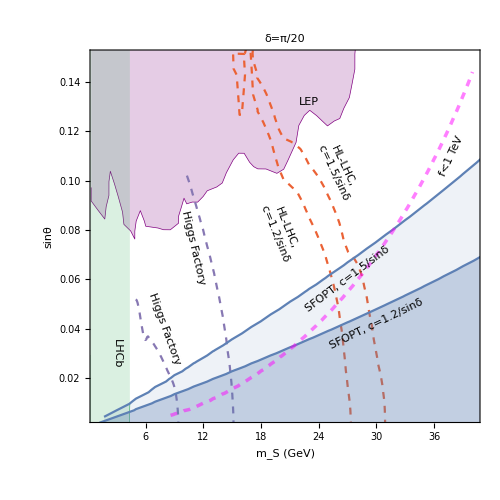

```mathematica
Show[LEP1996,LHCb,Higgsfactory,Higgsfactory2,exoticprosp,exoticprosp‵15,c12‵δpi20‵strength‵plot,c15‵δpi20‵strength‵plot,c12‵δpi20‵f‵plot,PlotRange->{{1,40},{0.005,0.15}},BaseStyle->{FontSize->22,FontFamily->"Times"},Frame->True,BoundaryStyle->None,FrameLabel->{Style["m_S (GeV)",FontFamily->"Times",FontSize->24],Style["sinθ",FontFamily->"Times",FontSize->24]},LabelStyle->{Black},FrameTicksStyle->Directive[FontFamily->"Times",FontSize->24],PlotRangePadding->None,ImageSize->500,AspectRatio->1,PlotLabel->Style["δ=π/20",FontFamily->"Times",FontSize->26],Epilog->{Inset[Rotate[Framed[Style["SFOPT, c=1.2/sinδ",FontFamily->"Times",FontSize->24,FontColor->ColorData[97,1]],FrameStyle->None],26Degree],{30,0.042}],Inset[Rotate[Framed[Style["SFOPT, c=1.5/sinδ",FontFamily->"Times",FontSize->24,FontColor->ColorData[97,1]],FrameStyle->None],37 Degree],{27,0.06}],
Inset[Rotate[Framed[Style["Higgs Factory",ColorData[97,5],FontSize->22],FrameStyle->None],-77Degree],{11,0.073}],Inset[Rotate[Framed[Style["Higgs Factory",ColorData[97,5],FontSize->22],FrameStyle->None],-70Degree],{8,0.04}],Inset[Rotate[Framed[Style["HL-LHC,\n c=1.2/sinδ",ColorData[97,4],FontSize->22],FrameStyle->None],-68Degree],{20,0.08}],Inset[Rotate[Framed[Style["HL-LHC,\n c=1.5/sinδ",ColorData[97,4],FontSize->22],FrameStyle->None],-65Degree],{26,0.105}],Inset[Framed[Style["LEP",FontFamily->"Times",FontSize->22,Purple],FrameStyle->None],{23,0.132}],Inset[Rotate[Framed[Style["LHCb",ColorData[97,15],FontSize->22],FrameStyle->None],-90Degree],{3,0.03}],Inset[Rotate[Framed[Style["f<1 TeV",Magenta,FontSize->22],FrameStyle->None],65Degree],{37.8,0.11}]}]
```

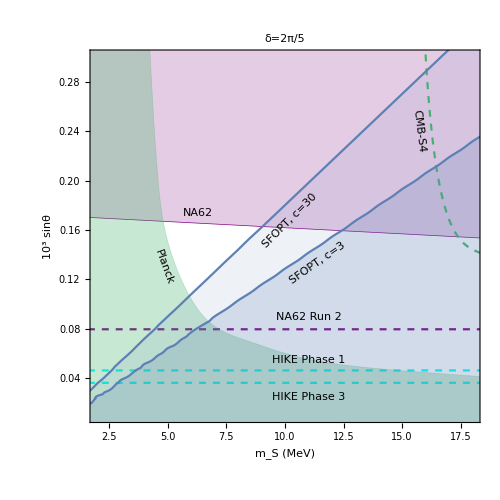

```mathematica
Show[Kaondecay1,Kaondecay2,CMB‵perspect,Planck,c30‵δ2pi5‵MeV‵strength‵plot,c3‵δ2pi5‵MeV‵strength‵plot,PlotRange->{{2,18},{0.01,0.3}},BaseStyle->{FontSize->22,FontFamily->"Times"},Frame->True,BoundaryStyle->None,FrameLabel->{Style["m_S (MeV)",FontFamily->"Times",FontSize->24],Style["10^3 sinθ",FontFamily->"Times",FontSize->24]},LabelStyle->{Black},FrameTicksStyle->Directive[FontFamily->"Times",FontSize->24],PlotRangePadding->None,ImageSize->500,AspectRatio->1,PlotLabel->Style["δ=2π/5",FontFamily->"Times",FontSize->26],Epilog->{Inset[Framed[Style["NA62",Purple, FontFamily->"Times",FontSize->24],FrameStyle->None],{6.3,0.174}],Inset[Rotate[Framed[Style["Planck",ColorData[97,15],FontFamily->"Times",FontSize->24],FrameStyle->None],-70 Degree],{4.85,0.13}],Inset[Rotate[Framed[Style["CMB-S4",ColorData[97,15],FontFamily->"Times",FontSize->24],FrameStyle->None],-83Degree],{15.7,0.24}],Inset[Rotate[Framed[Style["NA62 Run 2",Purple,FontFamily->"Times",FontSize->24],FrameStyle->None],0Degree],{11,0.09}],Inset[Rotate[Framed[Style["HIKE Phase 1",Darker[Cyan],FontFamily->"Times",FontSize->24],FrameStyle->None],0Degree],{11,0.055}],Inset[Rotate[Framed[Style["HIKE Phase 3",Darker[Cyan],FontFamily->"Times",FontSize->24],FrameStyle->None],0Degree],{11,0.025}],Inset[Rotate[Framed[Style["SFOPT, c=3",ColorData[97,1],FontFamily->"Times",FontSize->24],FrameStyle->None],35Degree],{11.4,0.133}],Inset[Rotate[Framed[Style["SFOPT, c=30",ColorData[97,1],FontFamily->"Times",FontSize->24],FrameStyle->None],45Degree],{10.2,0.168}]}]
```

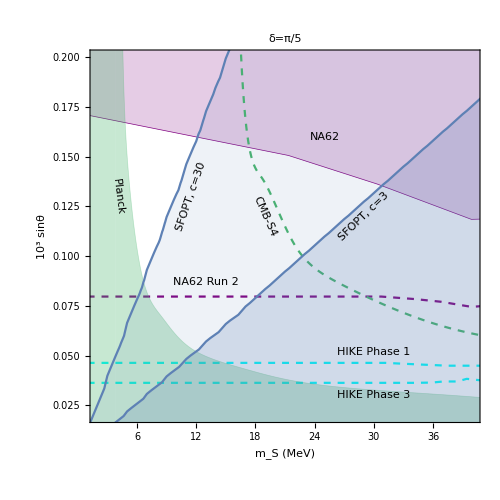

```mathematica
Show[Kaondecay1,Kaondecay2,CMB‵perspect,Planck,c3‵δpi5‵MeV‵strength‵plot,c30‵δpi5‵MeV‵strength‵plot,PlotRange->{{2,40},{0.02,0.2}},BaseStyle->{FontSize->22,FontFamily->"Times"},Frame->True,BoundaryStyle->None,FrameLabel->{Style["m_S (MeV)",FontFamily->"Times",FontSize->24],Style["10^3 sinθ",FontFamily->"Times",FontSize->24]},LabelStyle->{Black},FrameTicksStyle->Directive[FontFamily->"Times",FontSize->24],PlotRangePadding->None,ImageSize->500,AspectRatio->1,PlotLabel->Style["δ=π/5",FontFamily->"Times",FontSize->26],Epilog->{Inset[Framed[Style["NA62",Purple, FontFamily->"Times",FontSize->24],FrameStyle->None],{25,0.16}],Inset[Rotate[Framed[Style["SFOPT, c=3",ColorData[97,1],FontFamily->"Times",FontSize->24],FrameStyle->None],44Degree],{29,0.12}],Inset[Rotate[Framed[Style["SFOPT, c=30",ColorData[97,1],FontFamily->"Times",FontSize->24],FrameStyle->None],71Degree],{11.5,0.13}],Inset[Rotate[Framed[Style["Planck",ColorData[97,15],FontFamily->"Times",FontSize->24],FrameStyle->None],-83 Degree],{4.1,0.13}],Inset[Rotate[Framed[Style["CMB-S4",ColorData[97,15],FontFamily->"Times",FontSize->24],FrameStyle->None],-66Degree],{19,0.12}],Inset[Rotate[Framed[Style["NA62 Run 2",Purple,FontFamily->"Times",FontSize->24],FrameStyle->None],0Degree],{13,0.087}],Inset[Rotate[Framed[Style["HIKE Phase 1",Darker[Cyan],FontFamily->"Times",FontSize->24],FrameStyle->None],0Degree],{30,0.052}],Inset[Rotate[Framed[Style["HIKE Phase 3",Darker[Cyan],FontFamily->"Times",FontSize->24],FrameStyle->None],0Degree],{30,0.030}]}]
```

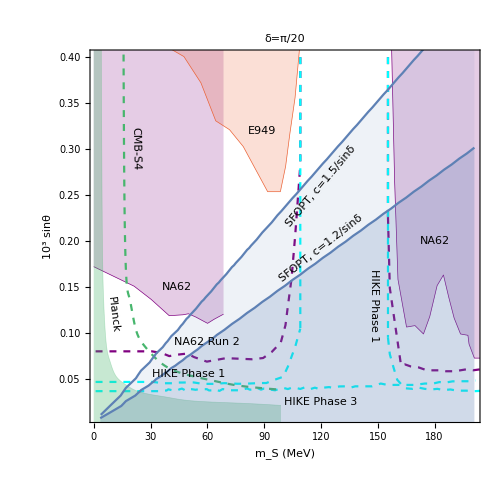

```mathematica
Show[Kaondecay1,Kaondecay2,CMB‵perspect,Planck,c12‵δpi20‵MeV‵strength‵plot,c15‵δpi20‵MeV‵strength‵plot,PlotRange->{{2,200},{0.01,0.4}},BaseStyle->{FontSize->22,FontFamily->"Times"},Frame->True,BoundaryStyle->None,FrameLabel->{Style["m_S (MeV)",FontFamily->"Times",FontSize->24],Style["10^3 sinθ",FontFamily->"Times",FontSize->24]},LabelStyle->{Black},FrameTicksStyle->Directive[FontFamily->"Times",FontSize->24],PlotRangePadding->None,ImageSize->500,AspectRatio->1,PlotLabel->Style["δ=π/20",FontFamily->"Times",FontSize->26],Epilog->{Inset[Framed[Style["NA62",Purple, FontFamily->"Times",FontSize->24],FrameStyle->None],{44,0.15}],Inset[Framed[Style["NA62",Purple, FontFamily->"Times",FontSize->24],FrameStyle->None],{180,0.2}],Inset[Rotate[Framed[Style["SFOPT, c=1.2/sinδ",ColorData[97,1],FontFamily->"Times",FontSize->24],FrameStyle->None],38Degree],{120,0.192}],Inset[Rotate[Framed[Style["SFOPT, c=1.5/sinδ",ColorData[97,1],FontFamily->"Times",FontSize->24],FrameStyle->None],50Degree],{120,0.26}],Inset[Rotate[Framed[Style["Planck",ColorData[97,15],FontFamily->"Times",FontSize->24],FrameStyle->None],-83 Degree],{10,0.12}],Inset[Rotate[Framed[Style["CMB-S4",ColorData[97,15],FontFamily->"Times",FontSize->24],FrameStyle->None],-89Degree],{22,0.3}],Inset[Rotate[Framed[Style["NA62 Run 2",Purple,FontFamily->"Times",FontSize->24],FrameStyle->None],0Degree],{60,0.09}],Inset[Rotate[Framed[Style["HIKE Phase 1",Darker[Cyan],FontFamily->"Times",FontSize->24],FrameStyle->None],0Degree],{50,0.055}],
Inset[Rotate[Framed[Style["HIKE Phase 1",Darker[Cyan],FontFamily->"Times",FontSize->24],FrameStyle->None],-90Degree],{148,0.13}],Inset[Rotate[Framed[Style["HIKE Phase 3",Darker[Cyan],FontFamily->"Times",FontSize->24],FrameStyle->None],0Degree],{120,0.024}],Inset[Rotate[Framed[Style["E949",ColorData[97,4],FontFamily->"Times",FontSize->24],FrameStyle->None],0Degree],{89,0.32}]}]
```

## BAU

Specific section for BAU. Just try to see the order of magnitude of the BAU from simple gauge boson coupling model.

```mathematica
α2=0.65^2/(4π);
s=2 π^2/45*100;
ΔS[A_,μSsq_,f_,δ_,h_,T_]:=f (ArcTan[(A(3(h^2-v^2)+T^2)Sin[δ])/(6f μSsq+A(3(h^2-v^2)+T^2)Cos[δ])]-ArcTan[(A(3(-v^2)+T^2)Sin[δ])/(6f μSsq+A(3(-v^2)+T^2)Cos[δ])]);
c30‵δ2pi5‵BAU‵data={#1,#2,3*20*α2^5/(#7*s*8.7*10^-11)ΔS[#4,#6,#7,2 π/5,1.2*#8*#9,#9]}&@@@c30‵δ2pi5‵data;
c3‵δ2pi5‵BAU‵data={#1,#2,3*20*α2^5/(#7*s*8.7*10^-11)ΔS[#4,#6,#7,2 π/5,1.2*#8*#9,#9]}&@@@c3‵δ2pi5‵data;
c30‵δpi5‵BAU‵data={#1,#2,3*20*α2^5/(#7*s*8.7*10^-11)ΔS[#4,#6,#7,π/5,1.2*#8*#9,#9]}&@@@c30‵δpi5‵data;
c3‵δpi5‵BAU‵data={#1,#2,3*20*α2^5/(#7*s*8.7*10^-11)ΔS[#4,#6,#7,π/5,1.2*#8*#9,#9]}&@@@c3‵δpi5‵data;
c12‵δpi20‵BAU‵data={#1,#2,3*20*α2^5/(#7*s*8.7*10^-11)ΔS[#4,#6,#7,π/20,1.2*#8*#9,#9]}&@@@c12‵δpi20‵data;
c15‵δpi20‵BAU‵data={#1,#2,3*20*α2^5/(#7*s*8.7*10^-11)ΔS[#4,#6,#7,π/20,1.2*#8*#9,#9]}&@@@c15‵δpi20‵data;
```

```mathematica
α2=0.65^2/(4π);
s=2 π^2/45*100;
ΔS[A_,μSsq_,f_,δ_,h_,T_]:=f (ArcTan[(A(3(h^2-v^2)+T^2)Sin[δ])/(6f μSsq+A(3(h^2-v^2)+T^2)Cos[δ])]-ArcTan[(A(3(-v^2)+T^2)Sin[δ])/(6f μSsq+A(3(-v^2)+T^2)Cos[δ])]);
c30‵δ2pi5‵BAU‵data={#1,#2,3*20*α2^5/(#7*s*8.7*10^-11)ΔS[#4,#6,#7,2 π/5,0.5*#9,#9]}&@@@c30‵δ2pi5‵data;
c3‵δ2pi5‵BAU‵data={#1,#2,3*20*α2^5/(#7*s*8.7*10^-11)ΔS[#4,#6,#7,2 π/5,0.5*#9,#9]}&@@@c3‵δ2pi5‵data;
c30‵δpi5‵BAU‵data={#1,#2,3*20*α2^5/(#7*s*8.7*10^-11)ΔS[#4,#6,#7,π/5,0.5*#9,#9]}&@@@c30‵δpi5‵data;
c3‵δpi5‵BAU‵data={#1,#2,3*20*α2^5/(#7*s*8.7*10^-11)ΔS[#4,#6,#7,π/5,0.5*#9,#9]}&@@@c3‵δpi5‵data;
c12‵δpi20‵BAU‵data={#1,#2,3*20*α2^5/(#7*s*8.7*10^-11)ΔS[#4,#6,#7,π/20,0.5*#9,#9]}&@@@c12‵δpi20‵data;
c15‵δpi20‵BAU‵data={#1,#2,3*20*α2^5/(#7*s*8.7*10^-11)ΔS[#4,#6,#7,π/20,0.5*#9,#9]}&@@@c15‵δpi20‵data;
```